```mathematica
ⅇ^34
```

ⅇ^34

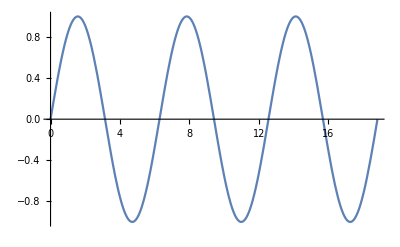

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
Factor[x^2  -x + 1]
```

1-x+x^2

# Mathematica Workshop @ SVNIT

Mano Prakash P (Student)

```mathematica
Factor[45 + 63x + 32x^2+16x^3+3x^4+x^5]
```

(1+x) (9+x^2) (5+2 x+x^2)

```mathematica
Evaluate [%]
```

(1+x) (9+x^2) (5+2 x+x^2)

```mathematica
Expand [%]
```

45+63 x+32 x^2+16 x^3+3 x^4+x^5

```mathematica
α + β
```

α+β

```mathematica
N[Pi, 200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

```mathematica
N[GoldenRatio, 200]
```

1.6180339887498948482045868343656381177203091798057628621354486227052604628189024497072072041893911374847540880753868917521266338622235369317931800607667263544333890865959395829056383226613199282902679

```mathematica
N[Sqrt[3], 200]
```

1.732050807568877293527446341505872366942805253810380628055806979451933016908800037081146186757248575675626141415406703029969945094998952478811655512094373648528093231902305582067974820101084674923265

```mathematica
PrimeQ[123456789]
```

False

```mathematica
PrimeQ[111119]
```

True

```mathematica
PrimeQ[1000001]
```

False

```mathematica
( 10 * Sqrt [((10.8 * 10^3)/300)])^3
```

216000.

```mathematica
D[Sin[2x], x]
```

2 Cos[2 x]

```mathematica
D[(1+x^2 + x^n), x]
```

```mathematica
2 x+n x^(-1+n)
```

```mathematica
D[Exp[x](x^2 + Sin[x*y]), x]
```

ⅇ^x (2 x+y Cos[x y])+ⅇ^x (x^2+Sin[x y])

```mathematica
D[(x^2 + y^2 + z^2)Exp[z], x]
```

2 ⅇ^z x

```mathematica
Integrate[1/x,x]
```

Log[x]

```mathematica
Integrate[a*x^2  + b*y^2 + 2x*y, x,y]
```

1/3 a x^3 y+(x^2 y^2)/2+1/3 b x y^3

```mathematica
NIntegrate[Exp[x]Sin[x^2], {x, -1 * Pi, Pi}]
```

4.65506

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,2}]
```

1.24706

```mathematica
FindMaximum[(x^n)* Exp[x] + y*Tan[x],x]
```

FindMaximum::nrnum: The function value -2.71828-1.55741 y is not a real number at {x} = {1.}.

FindMaximum[x^n Exp[x]+y Tan[x],x]

```mathematica
D[(x^n)* Exp[x] + y*Tan[x],x,y]
```

Sec[x]^2

```mathematica
NSolve[a*x^5 + 5*x^3 + b*x^2 + 10*x + 1 == 0 ,x]
```

{{x→Root[1.+10. #1+b #1^2+5. #1^3+a #1^5&,1]},{x→Root[1.+10. #1+b #1^2+5. #1^3+a #1^5&,2]},{x→Root[1.+10. #1+b #1^2+5. #1^3+a #1^5&,3]},{x→Root[1.+10. #1+b #1^2+5. #1^3+a #1^5&,4]},{x→Root[1.+10. #1+b #1^2+5. #1^3+a #1^5&,5]}}

```mathematica
f[x_,y_]:=(x^n)* Exp[x] + y*Tan[x];
DSolve[[f[x,y],x] == 0 , x,y];
```

Syntax::sntxb: Expression cannot begin with "[f[x,y],x]==0".

```mathematica
f[x_]:=Exp[x] + x;
DSolve[[f[x],x] == 0, x]
```

Syntax::sntxb: Expression cannot begin with "[f[x],x]==0".

```mathematica
Solve[x^3 - 1==0, x]
```

{{x→1},{x→-(-1)^(1/3)},{x→(-1)^(2/3)}}

```mathematica
Solve[x^3 + y^3 + 3*x*y ==10 && x^2 + 10*y==4,{x,y}]
```

{{x→Root2.19Root[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,1]2.191781757716066,y→1/10 (4-(Root2.19Root[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,1]2.191781757716066)^2)},{x→Root9.31Root[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,2]9.314628509548164,y→1/10 (4-(Root9.31Root[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,2]9.314628509548164)^2)},{x→Root-4.71-7.18 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,3]-4.714250812077725,y→1/10 (4-(Root-4.71-7.18 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,3]-4.714250812077725)^2)},{x→Root-4.71+7.18 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,4]-4.714250812077725,y→1/10 (4-(Root-4.71+7.18 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,4]-4.714250812077725)^2)},{x→Root-1.04-2.35 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,5]-1.0389543215543902,y→1/10 (4-(Root-1.04-2.35 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,5]-1.0389543215543902)^2)},{x→Root-1.04+2.35 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,6]-1.0389543215543902,y→1/10 (4-(Root-1.04+2.35 ⅈRoot[9936-1200 #1+48 #1^2-700 #1^3-12 #1^4+#1^6&,6]-1.0389543215543902)^2)}}

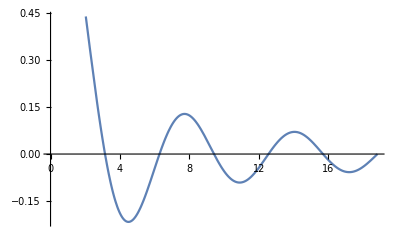

```mathematica
Plot[Sin[x]/x, {x,0, 6*Pi}]
```

```mathematica
Plot3D[x^2 + y^2 -1, {x,-3,3}, {y,-3,3}]
```

-Graphics3D-

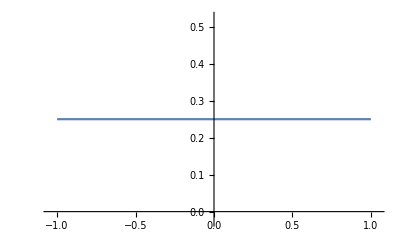

```mathematica
f[x_]:= Exp[ⅈ*2*x]/2;
Plot[f[x]*Conjugate[f[x]], {x, -1,1}]
```

```mathematica
?Fit
```

```mathematica
??Fit
```